```mathematica
ClearAll
```

ClearAll

```mathematica
h=10^(-10);
```

```mathematica
difn0=NDSolve[{x*y0''[x]+2*y0'[x]+x*(y0[x])^0==0,y0'[h]==0,y0[h]==1},y0,{x,0,10},StartingStepSize->1/10000,MaxStepFraction->1/10000];
```

NDSolve::ndsz: At x == 8.89438×10^-25, step size is effectively zero; singularity or stiff system suspected.

```mathematica
difn1=NDSolve[{x*y1''[x]+2*y1'[x]+x*(y1[x])^1==0,y1'[h]==0,y1[h]==1},y1,{x,0,10},StartingStepSize->1/10000,MaxStepFraction->1/10000];
```

NDSolve::ndsz: At x == 8.89438×10^-25, step size is effectively zero; singularity or stiff system suspected.

```mathematica
difn15=NDSolve[{x*y15''[x]+2*y15'[x]+x*(y15[x])^(1.5)==0,y15'[h]==0,y15[h]==1},y15,{x,0,10},StartingStepSize->1/10000,MaxStepFraction->1/10000];
```

NDSolve::ndsz: At x == 8.89438×10^-25, step size is effectively zero; singularity or stiff system suspected.

```mathematica
difn3=NDSolve[{x*y3''[x]+2*y3'[x]+x*(y3[x])^3==0,y3'[h]==0,y3[h]==1},y3,{x,0,10},StartingStepSize->1/10000,MaxStepFraction->1/10000];
```

NDSolve::ndsz: At x == 8.89438×10^-25, step size is effectively zero; singularity or stiff system suspected.

```mathematica
difn5=NDSolve[{x*y5''[x]+2*y5'[x]+x*(y5[x])^5==0,y5'[h]==0,y5[h]==1},y5,{x,0,10},StartingStepSize->1/10000,MaxStepFraction->1/10000];
```

NDSolve::ndsz: At x == 8.89438×10^-25, step size is effectively zero; singularity or stiff system suspected.

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(*RESULTADOS 1: APARTADO 1*)
```

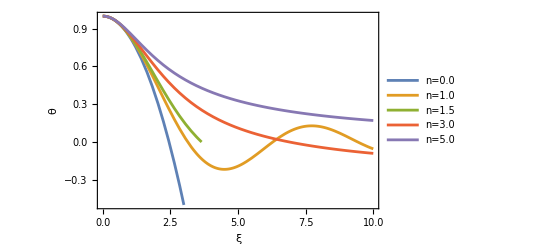

```mathematica
Plot[{Evaluate[y0[x]/.difn0 ],Evaluate[y1[x]/.difn1 ],Evaluate[y15[x]/.difn15 ],Evaluate[y3[x]/.difn3 ],Evaluate[y5[x]/.difn5 ]},{x,0,10},PlotLegends->{"n=0.0","n=1.0","n=1.5","n=3.0","n=5.0"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,10},{-0.5,1}},Frame->True,FrameLabel->{Style[ξ,16,Bold],Style[θ,16,Bold]}]
```

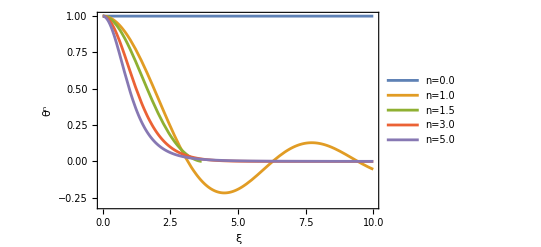

```mathematica
Plot[{Evaluate[(y0[x])^0/.difn0 ],Evaluate[(y1[x])^1/.difn1 ],Evaluate[(y15[x])^1.5/.difn15 ],Evaluate[(y3[x])^3/.difn3 ],Evaluate[(y5[x])^5/.difn5 ]},{x,0,10},PlotLegends->{"n=0.0","n=1.0","n=1.5","n=3.0","n=5.0"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,10},{-0.3,1}},Frame->True,FrameLabel->{Style[ξ,16,Bold],Style[θ^n,16,Bold]}]
```

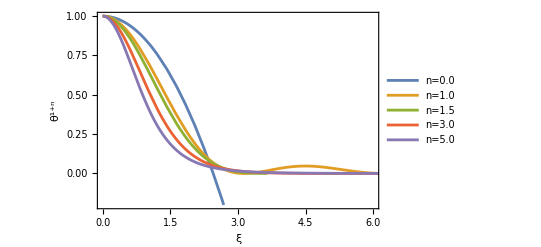

```mathematica
Plot[{Evaluate[(y0[x])^(1+0)/.difn0 ],Evaluate[(y1[x])^(1+1)/.difn1 ],Evaluate[(y15[x])^(1.5+1)/.difn15 ],Evaluate[(y3[x])^(3+1)/.difn3 ],Evaluate[(y5[x])^(5+1)/.difn5 ]},{x,0,10},PlotLegends->{"n=0.0","n=1.0","n=1.5","n=3.0","n=5.0"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,6},{-0.2,1}},Frame->True,FrameLabel->{Style[ξ,16,Bold],Style[θ^(n+1),16,Bold]}]
```

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(*RESULTADOS 1: APARTADO 2 y 3*)
```

```mathematica
FindRoot[Evaluate[y0[x]/.difn0]==0,{x,2}]
```

{x→2.44949}

```mathematica
ξ10=2.4494897427117235;
```

```mathematica
FindRoot[Evaluate[y1[x]/.difn1]==0,{x,3}]
```

{x→3.14159}

```mathematica
ξ11=3.141592653560422;
```

```mathematica
FindRoot[Evaluate[y15[x]/.difn15]==0,{x,2.5}]
```

FindRoot::nlnum: The function value {«1»} is not a list of numbers with dimensions {1} at {x} = {3.65375+1.00539×10^-13 ⅈ}.

{x→3.6537+0. ⅈ}

```mathematica
ξ115=3.653703123541946;
```

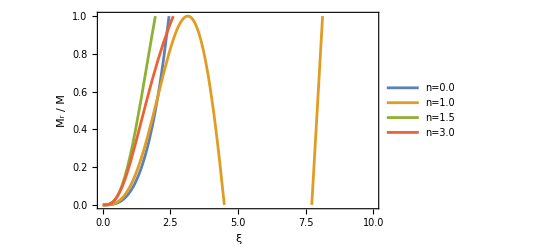

```mathematica
Plot[{(x/ξ10)^2*(Evaluate[y0'[x]/.difn0 ]/Evaluate[y0'[ξ10]/.difn0 ]),(x/ξ11)^2*(Evaluate[y1'[x]/.difn1 ]/Evaluate[y1'[ξ11]/.difn1 ]),Evaluate[(-x^2)*y3'[x]/.difn3 ],Evaluate[(-x^2)*y5'[x]/.difn5 ]},{x,0,10},PlotLegends->{"n=0.0","n=1.0","n=1.5","n=3.0","n=5.0"},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,10},{0,1}},Frame->True,FrameLabel->{Style[ξ,16,Bold],Style["Mᵣ / M",16,Bold]}]
```

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(*RESULTADOS 2: MODELO PARA EL SOL CON n=3*)
```

```mathematica
(*RESULTADOS 2: APARTADO 1*)
```

```mathematica
ρcent = (1.58*10^2)*1000;(*kg m^-3*)
```

```mathematica
Tcent=1.57*10^7; (*K*)
```

```mathematica
G=6.67430*10^(-11); (*en uds del SI*)
```

```mathematica
α[K_,n_]:=Sqrt[(K*(n+1)*ρcent^((1-n)/n))/(4*Pi*G)](*m*)
```

```mathematica
kB=1.3807*10^(-23);(*J K^-1*)
```

```mathematica
μ=1/(2*(0.7154)+(3/4)*(0.2703)+0.5*0.0142)
```

0.609524

```mathematica
mu=1.6605*10^(-27);(*kg*)
```

```mathematica
Kpolitrop=(kB*Tcent)/(μ*mu*(ρcent)^(1/3))
```

3.96172×10^9

```mathematica
FindRoot[Evaluate[y3[x]/.difn3]==0,{x,6.5}] (*Valor de Xi donde theta=0 (para n=3)*)
```

{x→6.89685}

```mathematica
ξ1=6.896848619542424
```

6.89685

```mathematica
RSol=α[Kpolitrop,3]*ξ1 (*m*)
```

5.54535×10^8

```mathematica
MSol=-4*Pi*(α[Kpolitrop,3])^3*ρcent*(ξ1)^2*Evaluate[y3'[ξ1]/.difn3]
```

{2.08293×10^30}

```mathematica
(*RESULTADOS 2: APARTADO 3*)
```

```mathematica
L0=(9.64*10^6)*Pi*(α[Kpolitrop,3]*100)^3*(ρcent/1000)^2*0.7154^2*((Tcent)/(10^6))^(-2/3) (*he pasado alpha a cm y rhocent a g/cm3. La sol está en ergios/s*)
```

3.2078×10^40

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(*RESULTADOS 2: APARTADO 2*)
```

```mathematica
(*gráfica M=M(r/R)*)
```

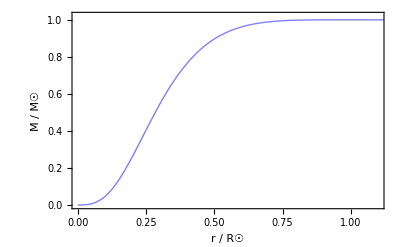

```mathematica
Plot[(-4*Pi*α[Kpolitrop,3]*ρcent*RSol^2*x^2*Evaluate[y3'[(RSol/α[Kpolitrop,3])*x]/.difn3 ])/MSol,{x,0,10},PlotStyle->{Blend[{Blue,White}],Thick},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,1.1},{0,1.02}},Frame->True,FrameLabel->{Style["r / R☉",16,Bold],Style["M / M☉",16,Bold]}]
```

```mathematica
(*gráfica rho=rho(r/R)*)
```

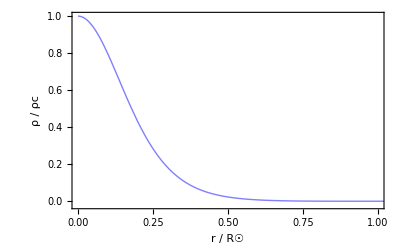

```mathematica
Plot[(ρcent*(Evaluate[y3[(RSol/α[Kpolitrop,3])*x]/.difn3 ])^3)/(ρcent),{x,0,10},PlotStyle->{Blend[{Blue,White}],Thick},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,1.0},{-0.02,1}},Frame->True,FrameLabel->{Style["r / R☉",16,Bold],Style["ρ / ρc",16,Bold]}]
```

```mathematica
(*gráfica T=T(r/R)*)
```

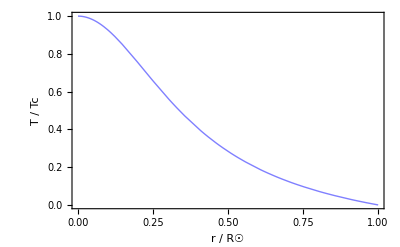

```mathematica
Plot[Evaluate[y3[(RSol/α[Kpolitrop,3])*x]/.difn3 ],{x,0,10},PlotStyle->{Blend[{Blue,White}],Thick},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,1.0},{0,1}},Frame->True,FrameLabel->{Style["r / R☉",16,Bold],Style["T / Tc",16,Bold]}]
```

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(*RESULTADOS 2: APARTADO 4*)
```

```mathematica
Ltot=L0*NIntegrate[(ξ^2)*(Evaluate[y3[ξ]]/.difn3)^(16/3)*Exp[-33.80*(Tcent/10^6)^(-1/3)*(Evaluate[y3[ξ]]/.difn3)^(-1/3)],{ξ,0,ξ1}]
```

{1.04905×10^34}

```mathematica
LSolEnErgs=Ltot
```

{1.04905×10^34}

```mathematica
LSolEnW=Ltot*10^(-7)
```

{1.04905×10^27}

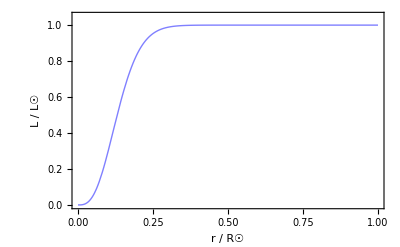

```mathematica
Plot[(L0*NIntegrate[(((RSol/α[Kpolitrop,3])*x)^2)*(Evaluate[y3[(RSol/α[Kpolitrop,3])*x]]/.difn3)^(16/3)*Exp[-33.80*(Tcent/10^6)^(-1/3)*(Evaluate[y3[(RSol/α[Kpolitrop,3])*x]]/.difn3)^(-1/3)]*(RSol/α[Kpolitrop,3]),{x,0,γ}])/LSolEnErgs,{γ,0,1},PlotStyle->{Blend[{Blue,White}],Thick},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotRange->{{0,1.0},{0,1.05}},Frame->True,FrameLabel->{Style["r / R☉",16,Bold],Style["L / L☉",16,Bold]}]
```